```mathematica
l=¬(p∧q);r=¬p∨¬q;
LogicalExpand[l]==LogicalExpand[r]
```

True

```mathematica
l=¬(p∨q);r=¬p∧¬q;
LogicalExpand[l]==LogicalExpand[r]
```

True

```mathematica
s=Select[Range[500],Mod[#,9]≠0&];
TableForm[Partition[s,5,5,1,{}],TableAlignments->Center]
```

1 | 2 | 3 | 4 | 5
6 | 7 | 8 | 10 | 11
12 | 13 | 14 | 15 | 16
17 | 19 | 20 | 21 | 22
23 | 24 | 25 | 26 | 28
29 | 30 | 31 | 32 | 33
34 | 35 | 37 | 38 | 39
40 | 41 | 42 | 43 | 44
46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 55 | 56
57 | 58 | 59 | 60 | 61
62 | 64 | 65 | 66 | 67
68 | 69 | 70 | 71 | 73
74 | 75 | 76 | 77 | 78
79 | 80 | 82 | 83 | 84
85 | 86 | 87 | 88 | 89
91 | 92 | 93 | 94 | 95
96 | 97 | 98 | 100 | 101
102 | 103 | 104 | 105 | 106
107 | 109 | 110 | 111 | 112
113 | 114 | 115 | 116 | 118
119 | 120 | 121 | 122 | 123
124 | 125 | 127 | 128 | 129
130 | 131 | 132 | 133 | 134
136 | 137 | 138 | 139 | 140
141 | 142 | 143 | 145 | 146
147 | 148 | 149 | 150 | 151
152 | 154 | 155 | 156 | 157
158 | 159 | 160 | 161 | 163
164 | 165 | 166 | 167 | 168
169 | 170 | 172 | 173 | 174
175 | 176 | 177 | 178 | 179
181 | 182 | 183 | 184 | 185
186 | 187 | 188 | 190 | 191
192 | 193 | 194 | 195 | 196
197 | 199 | 200 | 201 | 202
203 | 204 | 205 | 206 | 208
209 | 210 | 211 | 212 | 213
214 | 215 | 217 | 218 | 219
220 | 221 | 222 | 223 | 224
226 | 227 | 228 | 229 | 230
231 | 232 | 233 | 235 | 236
237 | 238 | 239 | 240 | 241
242 | 244 | 245 | 246 | 247
248 | 249 | 250 | 251 | 253
254 | 255 | 256 | 257 | 258
259 | 260 | 262 | 263 | 264
265 | 266 | 267 | 268 | 269
271 | 272 | 273 | 274 | 275
276 | 277 | 278 | 280 | 281
282 | 283 | 284 | 285 | 286
287 | 289 | 290 | 291 | 292
293 | 294 | 295 | 296 | 298
299 | 300 | 301 | 302 | 303
304 | 305 | 307 | 308 | 309
310 | 311 | 312 | 313 | 314
316 | 317 | 318 | 319 | 320
321 | 322 | 323 | 325 | 326
327 | 328 | 329 | 330 | 331
332 | 334 | 335 | 336 | 337
338 | 339 | 340 | 341 | 343
344 | 345 | 346 | 347 | 348
349 | 350 | 352 | 353 | 354
355 | 356 | 357 | 358 | 359
361 | 362 | 363 | 364 | 365
366 | 367 | 368 | 370 | 371
372 | 373 | 374 | 375 | 376
377 | 379 | 380 | 381 | 382
383 | 384 | 385 | 386 | 388
389 | 390 | 391 | 392 | 393
394 | 395 | 397 | 398 | 399
400 | 401 | 402 | 403 | 404
406 | 407 | 408 | 409 | 410
411 | 412 | 413 | 415 | 416
417 | 418 | 419 | 420 | 421
422 | 424 | 425 | 426 | 427
428 | 429 | 430 | 431 | 433
434 | 435 | 436 | 437 | 438
439 | 440 | 442 | 443 | 444
445 | 446 | 447 | 448 | 449
451 | 452 | 453 | 454 | 455
456 | 457 | 458 | 460 | 461
462 | 463 | 464 | 465 | 466
467 | 469 | 470 | 471 | 472
473 | 474 | 475 | 476 | 478
479 | 480 | 481 | 482 | 483
484 | 485 | 487 | 488 | 489
490 | 491 | 492 | 493 | 494
496 | 497 | 498 | 499 | 500

```mathematica
f[x_]:=4 x^3+3 x^2-x+2
a=Collect[f[x+h],x];
s=Solve[Coefficient[a,x^2]==0,h]
(a/.s)[[1]]==0//Expand
```

{{h→-1/4}}

19/8-(7 x)/4+4 x^3==0

```mathematica
p=(x-1)(x-2)^2(x-3)^3
q=(x-1)^2(x-2)(x-3)^4
fact1=Factor[p]
```

(-3+x)^3 (-2+x)^2 (-1+x)

(-3+x)^4 (-2+x) (-1+x)^2

(-3+x)^3 (-2+x)^2 (-1+x)

```mathematica
fact2=Factor[q]
```

(-3+x)^4 (-2+x) (-1+x)^2

```mathematica
a=PolynomialGCD[p,q]
```

(-3+x)^3 (-2+x) (-1+x)

```mathematica
b=PolynomialLCM[p,q]
```

(-3+x)^4 (-2+x)^2 (-1+x)^2

```mathematica
Expand[a*b]==Expand[p*q]
```

True

```mathematica
s={};k=1;
While[Prime[k]≤600,s=Append[s,Prime[k]];k++]
s1={};k=1;
While[Fibonacci[k]≤600,s1=Append[s1,Fibonacci[k]];k++]
Intersection[s,s1]
```

{2,3,5,13,89,233}

```mathematica
m={{2,1,1},{1,-1,2},{1,1,-1}};m1={{8,1,1},{1,-1,2},{4,1,-1}};
m2={{2,8,1},{1,1,2},{1,4,-1}};
m3={{2,1,8},{1,-1,1},{1,1,4}};
x=Det[m1]/Det[m];
y=Det[m2]/Det[m];
z=Det[m3]/Det[m];Print["The Solutionis","x=",x,"y=",y,"z=",z]
```

The Solutionisx=2y=3z=1

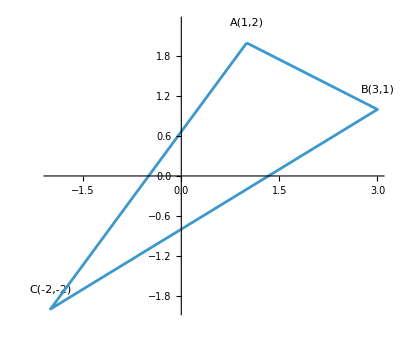

```mathematica
lst={{1,2},{3,1},{-2,-2},{1,2}};

pta=Graphics[Text["A(1,2)",{1,2.3}]];
ptb=Graphics[Text["B(3,1)",{3,1.3}]];
ptc=Graphics[Text["C(-2,-2)",{-2,-1.7}]];

g2=ListPlot[lst,Joined->True,AxesOrigin->{0,0},AspectRatio->Automatic];

Show[{pta,ptb,ptc,g2},AxesOrigin->{0,0},Axes->True,AspectRatio->Automatic]
```